```mathematica
SetDirectory[NotebookDirectory[]]
```

\\wsl.localhost\Ubuntu\home\shiyin\work\git\work\critical_region\LPA\fixpoint_v3\nu\mub0\buffer

```mathematica
fpi=Flatten[Import["./fpi.dat"]];
mpi=Flatten[Import["./mPion.dat"]];
msigma=Flatten[Import["./mSigma.dat"]];
T=Flatten[Import["./TMeV.dat"]];
```

```mathematica
Tc=T[[1]];
t=-(T-Tc)/Tc;
xi=1/msigma^2;
data=Transpose[{Log[t[[2;;Length[t]]]],Log[xi[[2;;Length[t]]]]}];
data2=Transpose[{Log[t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub0=Transpose[{Log[t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
b2mub0=Transpose[{Log[t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data2[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
```

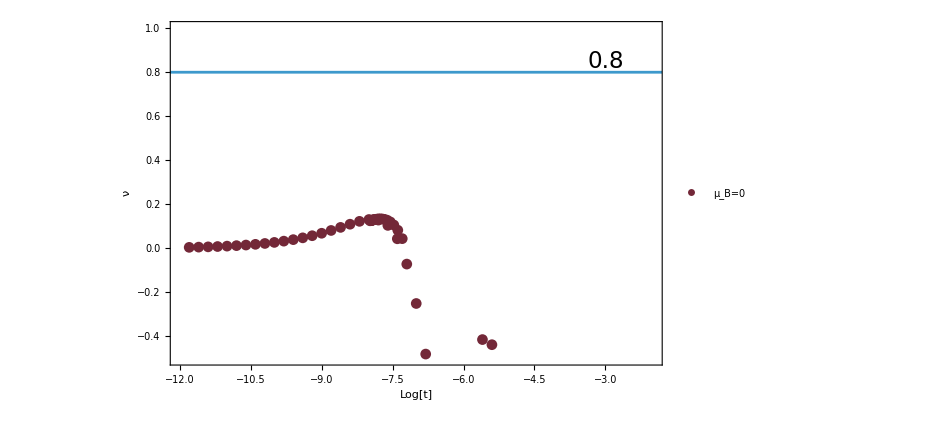

```mathematica
PlotT=Show[ListPlot[{b1mub0},
Frame->True,FrameLabel->{Style["Log[t]",25,FontFamily->"Times",Black],Style["ν",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.05}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_B=0"},LabelStyle->16],{0.23,0.32}],
PlotRange->{{-12,-2},{-0.5,1}},AxesOrigin->{-12,0.3},FrameTicksStyle->Directive[15,Black]],
ListLinePlot[{{-13,0.8},{10,0.8}}],ImageSize->700,Background->None,Epilog->{Text[Style["0.8",23],{-3,0.85}]}]
```

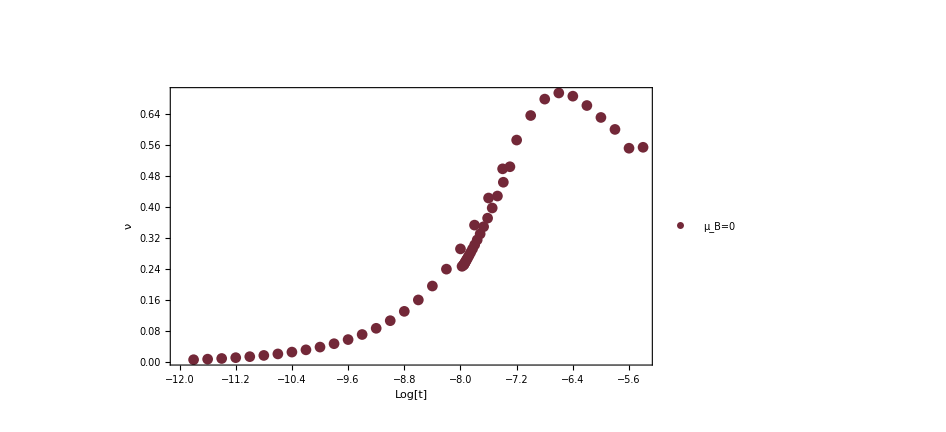

```mathematica
PlotT=Show[ListPlot[{b2mub0},
Frame->True,FrameLabel->{Style["Log[t]",25,FontFamily->"Times",Black],Style["ν",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.05}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_B=0"},LabelStyle->16],{0.23,0.32}],
PlotRange->All(*{{-12,-2},{0.6,0.9}}*),AxesOrigin->{-12,0.3},FrameTicksStyle->Directive[15,Black]],
ListLinePlot[{{-13,0.8},{10,0.8}}],ImageSize->700,Background->None,Epilog->{Text[Style["0.8",23],{-3,0.85}]}]
```